# 量子算法：QFT与Shor算法

## Quantum Fourier Transformation and Shor’s Algorithm

## 魏文杰

## 癸卯年十月廿一2023年12月3日13:19:02

```mathematica
<<Wolfram`QuantumFramework`
```

## 目录

量子算法预备

Deutsch算法

量子傅里叶变换

QFT的应用：相位估计

大数分解与Shor算法

Fourier变换的其他应用

总结：需要记住的关键知识点

参考文献和注释

## 量子算法预备

为什么要研究量子算法？

### 量子算法的应用清单1：应用领域2

凝聚态、核物理、高能物理、量子化学、组合(离散)优化、连续优化、密码学与密码分析、微分方程、金融、经典数据的机器学习

### 重点介绍的两种量子算法

基于量子傅里叶变换QFT的算法

相位估计 phase estimation

1994 Shor算法，多项式时间的因数分解算法。因数分解 ∈ BQP

离散对数问题 discrete log

隐藏子群问题 hidden subgroup

QFT

quantum field theory

quantum fluctuation theorem

quantum Fourier transformation

quantum fault tolerance

。。。

量子搜索算法

1996  Grover 算法对非结构化搜索问题进行了量子二次加速

推广：振幅放大 amplitude amplification

量子计算机要想对精确组合优化产生影响，必须做到以下两点之一：1）量子硬件的预期底层时钟速度和容错量子计算的开销取得巨大进步；或 2）量子算法的开发大大超过Grover算法提供的四倍速度3。

### 其他量子算法

参见：量子算法动物园 以及综述 4

连续优化问题的相关算法：纳什均衡与线性规划问题

变分量子求解器 Variational Quantum Eigensolver

量子随机游走

1985 黑箱(oracle)算法：Deutsch 算法

更多黑箱算法：Deutsch-Jozsa、Bernstein-Vazirani 和 Simon 算法

量子通信协议：1984 Charles Bennett 和 Gilles Brassard 将量子理论应用于密码协议，并证明量子密钥分发(QKD)可以增强信息安全性

2023新纪录：千公里以上的QKD

量子模拟算法

1980s Richard Feynman：在量子计算机上模拟量子系统

1996  Seth Lloyd ：以小时间步长演化可以有效模拟任何包含少粒子相互作用的多体量子哈密顿量； 模拟所需的总时间呈多项式增长。另一个链接

新世代的攻防战：后(抗)量子加密 post-quantum cryptography

量子计算的威力：
BQP是否严格大于BPP？但愿存在某些问题是量子计算机的概率算法能高效解决，但是概率图灵机不能高效解决的
大规模的容错量子计算能否实现？

## Deutsch算法

### 量子并行：Deutsch 算法

黑箱问题：给定黑箱函数 f : {0,1}{0,1}，判断 f 是平衡型还是常数型

量子并行：量子计算机能同时（在同一个幺正变换中）计算函数 f(x) 在许多 x 处的值

-Graphics-

#### 平衡型函数 f (x) = x 或者 f(x)=x1

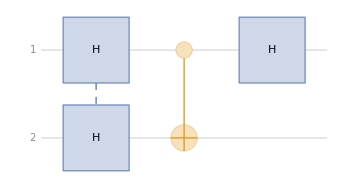

```mathematica
qc1 = QuantumCircuitOperator[{"H"->{1,2},"CNOT","H"}];(*设f(x) = x*)
qc1["Diagram"]
QuantumCircuitMultiwayGraph[qc1];
```

```mathematica
steps=ComposeList[qc1["Operators"],QuantumState[{0,1,0,0}]];
```

```mathematica
Grid[Transpose[{Style[#,Bold]&/@{"初态","经过前两个H门","(:7ecf:8fc7U)_f","经过最后的H门"},#["Formula"]&/@steps⟦;;⟧}],Frame->All,Alignment->Left]
```

初态 | 01
经过前两个H门 | 1/2 00-1/201+1/2 10-1/211
经过U_f | 1/2 00-1/201-1/210+1/2 11
经过最后的H门 | 1/(√2)10-1/(√2)11

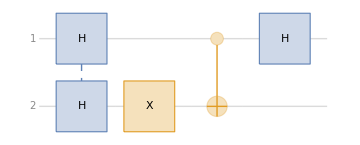

-1/(√2)10+1/(√2)11

```mathematica
qc2 = QuantumCircuitOperator[{"H"->{1,2},"X"->2,"CNOT","H"}];(*f(x)=x1*)
qc2["Diagram"]
qc2[QuantumState[{0,1,0,0}]]["Formula"]
```

#### 常数型函数 f(x)= 1 或 f(x)=0

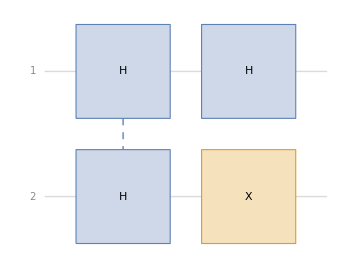

-1/(√2)00+1/(√2)01

```mathematica
qc3 = QuantumCircuitOperator[{"H"->{1,2},"X"->2,"H"}];(*f(x)=1*)
qc3["Diagram"]
qc3[QuantumState[{0,1,0,0}]]["Formula"]
```

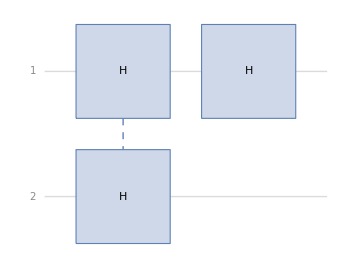

1/(√2)00-1/(√2)01

```mathematica
qc4 = QuantumCircuitOperator[{"H"->{1,2},"H"}];(*f(x)=1*)
qc4["Diagram"]
qc4[QuantumState[{0,1,0,0}]]["Formula"]
```

-Graphics-

根据第一个qubit的在计算基下的测量结果，我们就能知道函数是平衡型还是常数型，也即计算了f(0)f(1)的值，对于常数型f(0)f(1)=0，对于平衡型f(0)f(1)=1

每个量子线路都只使用了一次U_f，即只需要一次计算就完成了经典计算需要两次计算才能完成的任务

启发：对于那些经典计算获得的信息量超过问题的答案能够提供的信息量的问题（尝试计算信息量），也即经典计算存在计算冗余的问题，量子计算具有潜在的加速可能

判断平衡型和常数型的量子算法推广到 f 具有 n 个slot的情况，称为Deutsch-Jozsa算法，参见 Sec.1.4.4

### Deutsch-Jozsa算法

## 量子傅里叶变换

### 经典的离散傅里叶变换

傅里叶分析、调和分析：由基本波的叠加来表示其他函数或是信号

1/(√N)∑_(r=1)^N u_r e^(2π i(r-1)(s-1)/N) , s =1 , ... , N

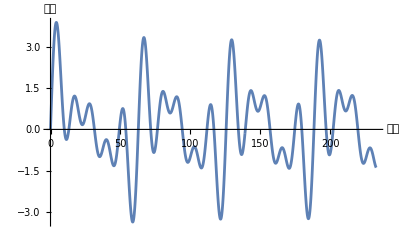

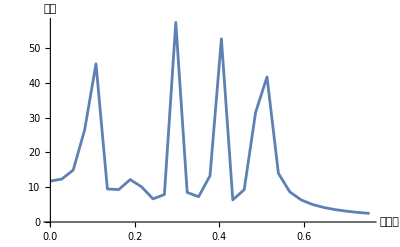

```mathematica
Clear[f];
num=13400;(*总采样点数*)
timespan=233;(*采样持续时间*)
bandwidth=num/(2timespan);(*采样率、带宽(实际上是不同的概念)*)
f[t_]:=(Sin[0.1 t]+E^(-0.03 t)Sin[0.2t]+Sin[0.3t]+Sin[0.4t]+Sin[0.5t]);
mat2=Table[f[timespan*i/num],{i,0,num}];
ListLinePlot[Table[{timespan*i/num,f[timespan*i/num]},{i,0,num}],AxesLabel->{"时间","振幅"}]
four=Abs@Fourier@mat2;
da=Table[{(k*2*Pi)/timespan,four[[k+1]]},{k,0,bandwidth}];
ListLinePlot[da,PlotRange->All,AxesLabel->{"角频率","振幅"}]
```

### 量子 Fourier 变换

1/(√N)∑_(k=0)^(N-1) e^(2π i j k/N)u_k , j =0, ... , N-1

注意Fourier变换是线性变换，因此才有显然的量子类比

计算基的态 取代了数列的项  ，j_i 取零或一，在推导中，交替使用十进制和二进制两种表示方式。

约定：低位比特在线路图中靠上，在bracket中靠左，即，越靠上或越靠左的比特的索引序号越小。(这种约定导致做加法时向低位进位，01+01=10)

序列的长度为 N，至少需要多少比特？1+ [log_2 N]

写成大家喜闻乐见的bracket算符形式和矩阵形式

-Graphics-

-Graphics--Graphics-

特殊的范德蒙德矩阵，只要设 -Graphics-

-Graphics-

因式分解

-Graphics-

作为上式的推论，计算基中的态Fourier变换后是直积态。

上式右边的因式分解能帮助我们利用简单的门逻辑门设计 Fourier 变换线路。

证明如下

-Graphics-

最后一行可以利用指数函数的周期性进行化简，定义二进制数的小数部分

二进制小数乘二，小数点向右跳一位

二进制小数除以二，小数点向左跳一位

上述算法被称为快速傅里叶变换FFT

Fourier 变换的结果被储存在概率幅中，无法直接读取，只能用统计方法推断，需要用更加巧妙的方法加以利用。

检验QFT的幺正性

```mathematica
Block[{n,m},n=3;m=1/(√2)^n(VandermondeMatrix[Table[o^k,{k,1,2^n}]]//Normal)/.o->E^(I (2π)/2^n)//N;
(m//Inverse//N//Chop)==ConjugateTranspose[m]]
```

True

### 量子线路

#### 两比特 N =2^n = 4 , n = 2

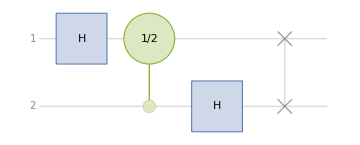

(1/2 | 1/2 | 1/2 | 1/2
1/2 | ⅈ/2 | -1/2 | -ⅈ/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -ⅈ/2 | -1/2 | ⅈ/2)

```mathematica
qft2=QuantumCircuitOperator["Fourier"];
%//TraditionalForm
qft2["Matrix"]//Normal//MatrixForm
```

```mathematica
qft2["Operators"][[2]]["Matrix"]//Normal//MatrixForm(*第二比特控制第一比特的控制S门，Subscript[CS, 2->1]，Subscript[实际上CS, 2->1] = Subscript[CS, 1->2]*)
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ)

```mathematica
qft2steps=ComposeList[qft2["Operators"],QuantumState[{0,1,0,0}]];
Grid[Transpose[{Style[#,Bold]&/@{"初态","(:7ecf:8fc7H)_1门","经过CU","(:7ecf:8fc7H)_2门","经过SWAP"},#["Formula"]&/@qft2steps⟦;;⟧}],Frame->All,Alignment->Left]
```

初态 | 01
经过H_1门 | 1/(√2)01+1/(√2)11
经过CU | 1/(√2)01+ⅈ/(√2)11
经过H_2门 | 1/2 00-1/201+ⅈ/2 10-ⅈ/211
经过SWAP | 1/2 00+ⅈ/2 01-1/210-ⅈ/211

```mathematica
Fourier[{0,1,0,0}]//Rationalize(*初态等效的经典输入*)
%//InverseFourier//Rationalize
```

{1/2,ⅈ/2,-1/2,-ⅈ/2}

{0,1,0,0}

#### 四比特

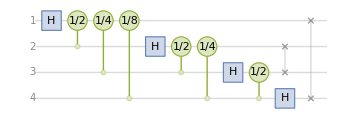

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/4)),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^((ⅈ π)/8))}

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(1/8) | (-1)^(1/4) | (-1)^(3/8) | ⅈ | (-1)^(5/8) | (-1)^(3/4) | (-1)^(7/8) | -1 | -(-1)^(1/8) | -(-1)^(1/4) | -(-1)^(3/8) | -ⅈ | -(-1)^(5/8) | -(-1)^(3/4) | -(-1)^(7/8)
1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4) | 1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4)
1 | (-1)^(3/8) | (-1)^(3/4) | -(-1)^(1/8) | -ⅈ | -(-1)^(7/8) | (-1)^(1/4) | (-1)^(5/8) | -1 | -(-1)^(3/8) | -(-1)^(3/4) | (-1)^(1/8) | ⅈ | (-1)^(7/8) | -(-1)^(1/4) | -(-1)^(5/8)
1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ
1 | (-1)^(5/8) | -(-1)^(1/4) | -(-1)^(7/8) | ⅈ | -(-1)^(1/8) | -(-1)^(3/4) | (-1)^(3/8) | -1 | -(-1)^(5/8) | (-1)^(1/4) | (-1)^(7/8) | -ⅈ | (-1)^(1/8) | (-1)^(3/4) | -(-1)^(3/8)
1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4) | 1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4)
1 | (-1)^(7/8) | -(-1)^(3/4) | (-1)^(5/8) | -ⅈ | (-1)^(3/8) | -(-1)^(1/4) | (-1)^(1/8) | -1 | -(-1)^(7/8) | (-1)^(3/4) | -(-1)^(5/8) | ⅈ | -(-1)^(3/8) | (-1)^(1/4) | -(-1)^(1/8)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -(-1)^(1/8) | (-1)^(1/4) | -(-1)^(3/8) | ⅈ | -(-1)^(5/8) | (-1)^(3/4) | -(-1)^(7/8) | -1 | (-1)^(1/8) | -(-1)^(1/4) | (-1)^(3/8) | -ⅈ | (-1)^(5/8) | -(-1)^(3/4) | (-1)^(7/8)
1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4) | 1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4)
1 | -(-1)^(3/8) | (-1)^(3/4) | (-1)^(1/8) | -ⅈ | (-1)^(7/8) | (-1)^(1/4) | -(-1)^(5/8) | -1 | (-1)^(3/8) | -(-1)^(3/4) | -(-1)^(1/8) | ⅈ | -(-1)^(7/8) | -(-1)^(1/4) | (-1)^(5/8)
1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ
1 | -(-1)^(5/8) | -(-1)^(1/4) | (-1)^(7/8) | ⅈ | (-1)^(1/8) | -(-1)^(3/4) | -(-1)^(3/8) | -1 | (-1)^(5/8) | (-1)^(1/4) | -(-1)^(7/8) | -ⅈ | -(-1)^(1/8) | (-1)^(3/4) | (-1)^(3/8)
1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4) | 1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4)
1 | -(-1)^(7/8) | -(-1)^(3/4) | -(-1)^(5/8) | -ⅈ | -(-1)^(3/8) | -(-1)^(1/4) | -(-1)^(1/8) | -1 | (-1)^(7/8) | (-1)^(3/4) | (-1)^(5/8) | ⅈ | (-1)^(3/8) | (-1)^(1/4) | (-1)^(1/8))

```mathematica
qft4=QuantumCircuitOperator[{"Fourier",4}];
%["Diagram"](*最后交换高低位约定*)
(#["Matrix"]//Normal//MatrixForm)&/@(qft4["Operators"][[2;;4]])(*qft4的第二到到第四个算符*)
4 qft4["Matrix"]//Normal//FullSimplify//MatrixForm
```

```mathematica
ω=E^((2π I)/2^4);
Table[ω^(i j),{i,0,15},{j,0,15}] //Normal//FullSimplify//MatrixForm(*根据前述公式*)
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | (-1)^(1/8) | (-1)^(1/4) | (-1)^(3/8) | ⅈ | (-1)^(5/8) | (-1)^(3/4) | (-1)^(7/8) | -1 | -(-1)^(1/8) | -(-1)^(1/4) | -(-1)^(3/8) | -ⅈ | -(-1)^(5/8) | -(-1)^(3/4) | -(-1)^(7/8)
1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4) | 1 | (-1)^(1/4) | ⅈ | (-1)^(3/4) | -1 | -(-1)^(1/4) | -ⅈ | -(-1)^(3/4)
1 | (-1)^(3/8) | (-1)^(3/4) | -(-1)^(1/8) | -ⅈ | -(-1)^(7/8) | (-1)^(1/4) | (-1)^(5/8) | -1 | -(-1)^(3/8) | -(-1)^(3/4) | (-1)^(1/8) | ⅈ | (-1)^(7/8) | -(-1)^(1/4) | -(-1)^(5/8)
1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ
1 | (-1)^(5/8) | -(-1)^(1/4) | -(-1)^(7/8) | ⅈ | -(-1)^(1/8) | -(-1)^(3/4) | (-1)^(3/8) | -1 | -(-1)^(5/8) | (-1)^(1/4) | (-1)^(7/8) | -ⅈ | (-1)^(1/8) | (-1)^(3/4) | -(-1)^(3/8)
1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4) | 1 | (-1)^(3/4) | -ⅈ | (-1)^(1/4) | -1 | -(-1)^(3/4) | ⅈ | -(-1)^(1/4)
1 | (-1)^(7/8) | -(-1)^(3/4) | (-1)^(5/8) | -ⅈ | (-1)^(3/8) | -(-1)^(1/4) | (-1)^(1/8) | -1 | -(-1)^(7/8) | (-1)^(3/4) | -(-1)^(5/8) | ⅈ | -(-1)^(3/8) | (-1)^(1/4) | -(-1)^(1/8)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -(-1)^(1/8) | (-1)^(1/4) | -(-1)^(3/8) | ⅈ | -(-1)^(5/8) | (-1)^(3/4) | -(-1)^(7/8) | -1 | (-1)^(1/8) | -(-1)^(1/4) | (-1)^(3/8) | -ⅈ | (-1)^(5/8) | -(-1)^(3/4) | (-1)^(7/8)
1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4) | 1 | -(-1)^(1/4) | ⅈ | -(-1)^(3/4) | -1 | (-1)^(1/4) | -ⅈ | (-1)^(3/4)
1 | -(-1)^(3/8) | (-1)^(3/4) | (-1)^(1/8) | -ⅈ | (-1)^(7/8) | (-1)^(1/4) | -(-1)^(5/8) | -1 | (-1)^(3/8) | -(-1)^(3/4) | -(-1)^(1/8) | ⅈ | -(-1)^(7/8) | -(-1)^(1/4) | (-1)^(5/8)
1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ
1 | -(-1)^(5/8) | -(-1)^(1/4) | (-1)^(7/8) | ⅈ | (-1)^(1/8) | -(-1)^(3/4) | -(-1)^(3/8) | -1 | (-1)^(5/8) | (-1)^(1/4) | -(-1)^(7/8) | -ⅈ | -(-1)^(1/8) | (-1)^(3/4) | (-1)^(3/8)
1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4) | 1 | -(-1)^(3/4) | -ⅈ | -(-1)^(1/4) | -1 | (-1)^(3/4) | ⅈ | (-1)^(1/4)
1 | -(-1)^(7/8) | -(-1)^(3/4) | -(-1)^(5/8) | -ⅈ | -(-1)^(3/8) | -(-1)^(1/4) | -(-1)^(1/8) | -1 | (-1)^(7/8) | (-1)^(3/4) | (-1)^(5/8) | ⅈ | (-1)^(3/8) | (-1)^(1/4) | (-1)^(1/8))

```mathematica
qft4[QuantumState["0001"]+QuantumState["0011"]]["Matrix"]//Normal//Flatten//N(*为了让结果更好看，没有归一化*)
%//InverseFourier//Chop
```

{0.5,0.326641+0.326641 ⅈ,0.+0.353553 ⅈ,-0.135299+0.135299 ⅈ,0.,0.135299+0.135299 ⅈ,0.+0.353553 ⅈ,-0.326641+0.326641 ⅈ,-0.5,-0.326641-0.326641 ⅈ,0.-0.353553 ⅈ,0.135299-0.135299 ⅈ,0.,-0.135299-0.135299 ⅈ,0.-0.353553 ⅈ,0.326641-0.326641 ⅈ}

{0,1.,0,1.,0,0,0,0,0,0,0,0,0,0,0,0}

#### n比特情形分析

检验：下面的电路除了高低位相反以外，实现了Fourier变换

-Graphics-

-Graphics-

## QFT的应用：相位估计

-Graphics-

#### 例：单比特的幺正算符的相位估计

当二进制数完美时，相位估计算法产生的估计值就是精确值

```mathematica
ϕ=1./4+1/8;(*完美的二进制小数，有限的二进制小数*)
%//Rationalize
BaseForm[ϕ,2]
u=QuantumOperator[{"Phase",2π Rationalize@ϕ}];
%//TraditionalForm//Chop
```

3/8

0.011_2

00+ⅇ^((3 ⅈ π)/4)11

```mathematica
Eigensystem[u["Matrix"]]//ComplexExpand(*本征值和本征态*)
AbsArg[%[[1,2]]](*模长和幅角*)
```

{{1,-(1-ⅈ)/(√2)},{{1,0},{0,1}}}

{1,(3 π)/4}

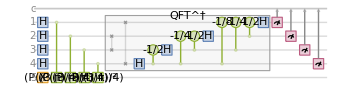

```mathematica
pe=QuantumCircuitOperator[{"PhaseEstimation",u,4}];
%["Diagram"](*第一个寄存器制备均匀叠加态，第二个寄存器制备U本征态，作用CU^k 若干次，做反傅里叶变换，测量第一个寄存器*)
```

```mathematica
-Graphics-//InputForm
```

Graphics[{EdgeForm[RGBColor[0.560181, 0.691569, 0.194885]], 
  FaceForm[{RGBColor[0.560181, 0.691569, 0.194885], Opacity[0.3]}], 
  GeometricTransformation[Inset[Style["P"[(3*Pi)/4]^8, FontFamily -> "Roboto", FontSize -> 11, 
     FontColor -> GrayLevel[0], Background -> GrayLevel[0, 0]], {2., -5.}], 
   {{{1, 0}, {0, 1}}, Center}]}, ImageSize -> {46.15780445969126, Automatic}]

```mathematica
label[x_]:=Graphics[{EdgeForm[RGBColor[0.560181,0.691569,0.194885]],FaceForm[{RGBColor[0.560181,0.691569,0.194885],Opacity[0.3]}],GeometricTransformation[Inset[Style["P"[(3*Pi)/4]^x,FontFamily->"Roboto",FontSize->11,FontColor->GrayLevel[0],Background->GrayLevel[0,0]],{2.,-5.}],{{{1,0},{0,1}},Center}]},ImageSize->{46.15780445969126,Automatic}](*制作一个标签*)
```

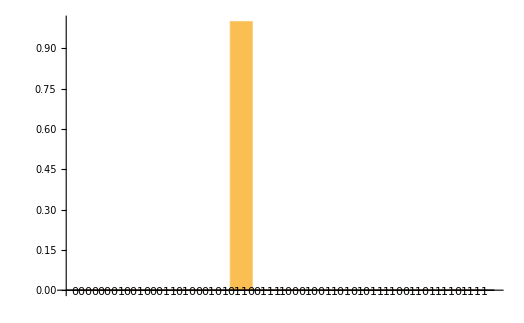

```mathematica
pe[QuantumState["00000"]]["ProbabilityPlot"]
```

相位估计作用顺序相反，但是等价（作为幺正算符完全相等）的线路

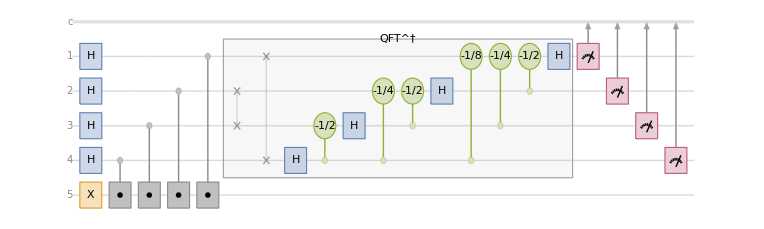

```mathematica
pe1=QuantumCircuitOperator[{"H"->1,"H"->2,"H"->3,"H"->4,"X"->5,Sequence@@Table[QuantumOperator[{"Controlled",QuantumOperator[MatrixPower[u["Matrix"],2^(k-1)],"Label"->label[2^(k-1)]]}]->{5-k,5},{k,1,4}],QuantumCircuitOperator[{"InverseFourier",4}],{1},{2},{3},{4}}];
%//TraditionalForm
```

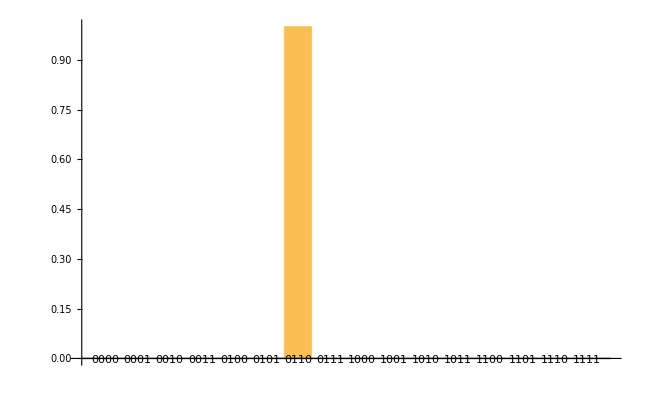

```mathematica
pe1[QuantumState["00000"]]["ProbabilityPlot"]
```

```mathematica
pe1==pe
```

True

```mathematica
pe["Matrix"]-pe1["Matrix"]//Normal//N//Re;
```

等价的原因如下：

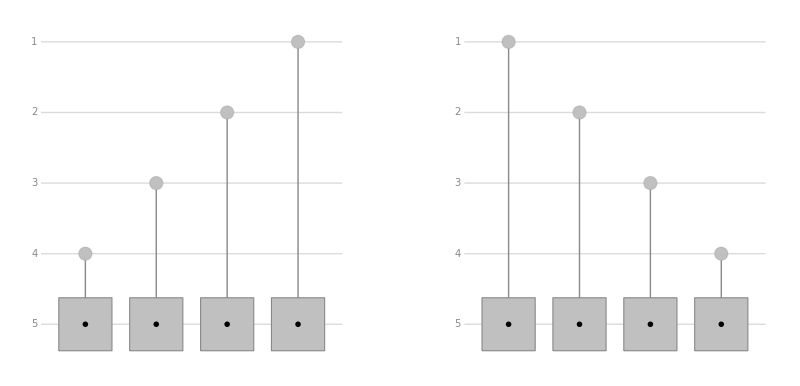

True

```mathematica
cu1=QuantumCircuitOperator[Table[QuantumOperator[{"Controlled",QuantumOperator[MatrixPower[u["Matrix"],2^(k-1)],"Label"->label[2^(k-1)]]}]->{5-k,5},{k,1,4}]];
cu2=QuantumCircuitOperator[Table[QuantumOperator[{"Controlled",QuantumOperator[MatrixPower[u["Matrix"],2^(4-k)],"Label"->label[2^(4-k)]]}]->{k,5},{k,1,4}]];
GraphicsRow[{cu1//TraditionalForm,"=",
cu2//TraditionalForm}]
cu1==cu2
cu1["Matrix"]-cu2["Matrix"]//Chop//Normal;
```

另外，有下面的等式

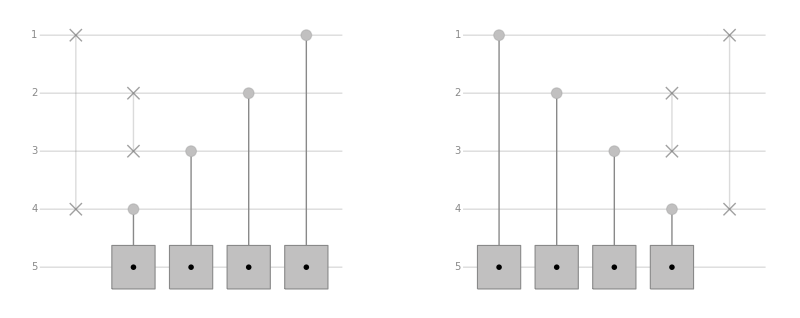

True

```mathematica
cu3=QuantumCircuitOperator[{"SWAP"->{1,4},"SWAP"->{2,3},Sequence@@Table[QuantumOperator[{"Controlled",QuantumOperator[MatrixPower[u["Matrix"],2^(k-1)],"Label"->label[2^(k-1)]]}]->{5-k,5},{k,1,4}]}];
cu4=QuantumCircuitOperator[{Sequence@@Table[QuantumOperator[{"Controlled",QuantumOperator[MatrixPower[u["Matrix"],2^(k-1)],"Label"->label[2^(k-1)]]}]->{k,5},{k,1,4}],"SWAP"->{2,3},"SWAP"->{1,4}}];
GraphicsRow[{cu3//TraditionalForm,"=",
cu4//TraditionalForm}]
cu3==cu4
cu3["Matrix"]-cu4["Matrix"]//Chop//Normal//N;
```

当二进制数不完美时，估计值不等于精确值

```mathematica
ϕ=1./4+1/8+0.02;(*不完美的二进制数，即无限小数*)
BaseForm[ϕ,2]
u=QuantumOperator[{"Phase",2π ϕ}];
%//TraditionalForm//Chop
```

0.011001010001111010111_2

00+(-0.790155+0.612907 ⅈ)11

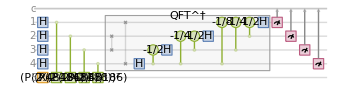

```mathematica
pe4=QuantumCircuitOperator[{"PhaseEstimation",u,4}];
%["Diagram"]
```

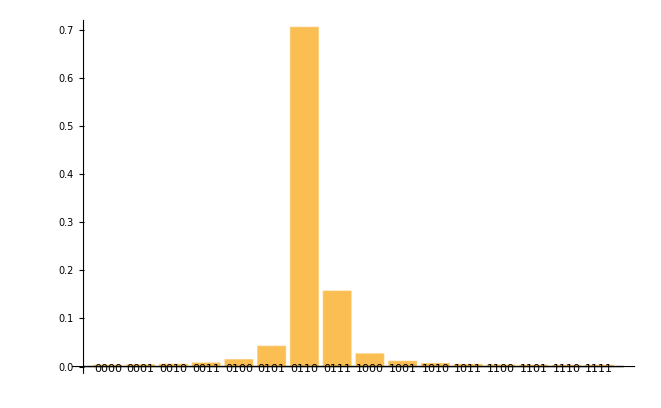

```mathematica
pe4[QuantumState["00000"]]["ProbabilityPlot"]
```

```mathematica
ϕ=1./4+1/8-0.02;(*不完美的二进制数，即无限小数*)
BaseForm[ϕ,2]
u=QuantumOperator[{"Phase",2π ϕ}];
%//TraditionalForm//Chop
```

0.010110101110000101001_2

00+(-0.612907+0.790155 ⅈ)11

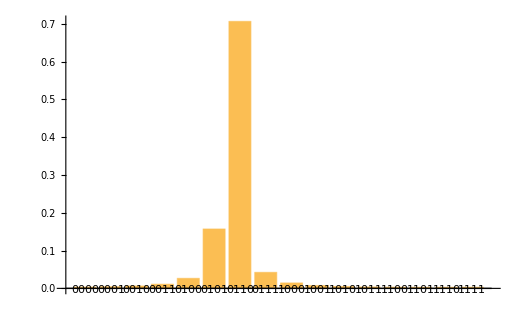

```mathematica
pe5=QuantumCircuitOperator[{"PhaseEstimation",u,4}];
pe5[QuantumState["00000"]]["ProbabilityPlot"]
```

#### 一般情况的分析

仍假设相位是完美的二进制小数

-Graphics-

-Graphics-

-Graphics-

二进制小数乘二，小数点向右跳一位

Q : 在相位估计中，为什么Mathematica的线路与书上的黑盒的作用的顺序是相反的？
A : SWAP被移动到了线路最左边被初态吸收，不同的控制门CU之间是相互对易的。

回顾：正Fourier变换

## 加法器

## 大数分解与Shor算法

#### 基本概念

GCD：greatest common divider

```mathematica
GCD[2,6,10]
```

2

```mathematica
DivisorSigma[1,2]==2 2
```

False

同余基本性质

-Graphics-

### 大数分解问题与RSA加密

Primality Testing and Factorization

大数分解的困难性保证了 RSA (Rivest-Shamir-Adleman) 公钥密码通信的安全性5。通用数域筛 (GNFS) 是已知用于分解大于 10^100 的整数的最高效的经典6算法。

Shor 算法高效地解决大数分解问题。

分解整数n ( 表示整数 n 仅需 [log_2 n]+1个比特 ) 的GNFS 计算步数

RSA 分解挑战

-Graphics-

CPU京东价格：7999

量子计算机的实用化标志：RSA数中任意一个的分解。(2045)

```mathematica
10^50+3
```

100000000000000000000000000000000000000000000000003

```mathematica
FactorInteger[10^50+3]//RepeatedTiming
```

{0.496153,{{19,1},{97,1},{283,1},{994327748569,1},{61236769827829,1},{3148809563627188687,1}}}

### 算法的主要步骤和说明

问题：N 是奇数且至少有两个质因子，找到N的一个非平凡因子。

-Graphics-

注意关于 y 的性质与它发挥的作用

-Graphics-

(3)的等价性

-Graphics-

分解 21

```mathematica
y=RandomInteger[{2,21}];(*任意选择一个与n互质的数*)
n=21(*被分解的数*);
r=FirstPosition[Table[(y^r-1)/n,{r,1,n}],_Integer][[1]](*暴力法求阶*)
GCD[y^(r/2)+1,n]
GCD[y^(r/2)-1,n]
```

NotFound

GCD[21,1+3^(NotFound/2)]

GCD[21,-1+3^(NotFound/2)]

### 用量子算法求阶

参考链接

将相位估计用在U ∈ U(2^n)上，它满足 ，在本节中通常以 x = 1（计算基中的第二个）为出发点。

通常，上式只定义了U在某个子空间上的行为，因此U不是唯一的，只要能制作出一个就可以完成Shor算法。

取 y = 3, x= 1 , N=35，作用 r 次之后会回到原来的态

```mathematica
lst=Block[{x,y,N},x=1;y=3;N=35;NestWhileList[Mod[y #,N]&,x y,#!=x&]]
r=%//Length
```

{3,9,27,11,33,29,17,16,13,4,12,1}

12

-Graphics--Graphics-

U的本征态是什么？通用方法：矩阵对角化

```mathematica
(rule[#1]=#2)&@@@Thread[Table[x,{x,0,11}]->lst](*或许可以写的更好看*)
```

{3,9,27,11,33,29,17,16,13,4,12,1}

```mathematica
Table[Annotation[v,{VertexSize->0.2+0.2Mod[v,5],VertexStyle->Hue[v/15,1,1]},VertexLabels->Thread[Table[x,{x,1,12}]->lst]],{v,0,r-1}];
```

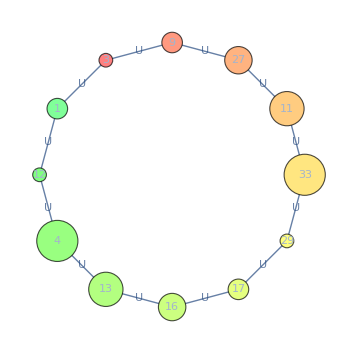

```mathematica
Graph[Table[Annotation[v,{VertexSize->0.2+0.1Mod[v,5],VertexStyle->Hue[v/30,0.5,2]},VertexLabels->Placed[rule[v],Center]],{v,0,r-1}],Table[v<->Mod[v+1,r],{v,0,r-1}],EdgeLabels->"U"]
```

显然，loop中各个态均匀叠加就可得到U的一个本征态

-Graphics-

-Graphics-

上述的例子是平凡的，U还有一些更有趣的本征值，注意到：如果等比例叠加的每个态前有一个正比于次序的因子，也能构成本征态。每一项在loop中跳一步再增加一个共同的相位因子 e^((2π i)/r) 得到下一项。

-Graphics-

-Graphics-

再做一点点推广，找到其他的本征态，s = 0, 1, 2, ... , r - 1

-Graphics-

-Graphics-

至此我们已经找到了loop中的态张成的子空间上的所有 r 个本征态。这些本征态的满足

-Graphics-

证明如下:

-Graphics-

开始计算求阶（U的相位估计）线路吧！( 求阶输入的态不是U的本征态，而是若干不同本征值的本征态的均匀叠加 )

-Graphics-

```mathematica
(*images=Import/@{"D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-12\\量子计算习题\\量子计算习题-286.jpg","D:\\WeChat Files\\wxid_rzkeqfbjyqqp12\\FileStorage\\File\\2023-12\\量子计算习题\\量子计算习题-287.jpg"}*)
```

-Graphics-

-Graphics-

概率分布

```mathematica
y=19;(*任意选择一个与n互质的数*)
n=21(*被分解的数*);
L=Floor[Log[2,n^2]//N]+1;(*需要的比特数*)
q=2^L;
r=FirstPosition[Table[(y^r-1)/n,{r,1,n}],_Integer][[1]](*暴力求阶*);
```

```mathematica
n^2<q<2 n^2
```

True

```mathematica
l=RandomChoice[Range[0,r-1]];(*随机地选择对第二个寄存器进行测量所得的结果*)
A=Floor[(q-l-1)/r];(*测量后的态的叠加项数-1*)
p[c_]:=Abs[1/(√(q(A+1)))Sum[E^(2Pi I (j r)c/q),{j,0,A}]]^2;(*f(c)*)
N[Sum[p[c],{c,0,q-1}],20]
```

1.

```mathematica
prb=Table[N[p[c],30],{c,1,q}];
```

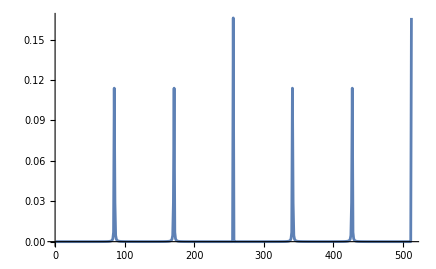

```mathematica
ListLinePlot[prb,PlotRange->All]
```

```mathematica
Position[PeakDetect[prb],1]/q//N
```

{{0.166016},{0.333984},{0.5},{0.666016},{0.833984},{1.}}

实际上线路中的QFT^†改为QFT，即逆变换改为正变换能得到完全相同的概率分布 Pr(k)

```mathematica
simConj[x_]:=(x//.{Abs[m_]^2:>Conjugate[m] m,Conjugate[m_+y_]:>Conjugate[m]+Conjugate[y],Conjugate[m_ y_]:>Conjugate[m] Conjugate[y]})/. Conjugate[k_]:>Simplify[Conjugate[k]]
```

```mathematica
Clear[k,L,A,r,q]
```

```mathematica
$Assumptions=(k|L|A|r|q)∈Integers&&k>0&&r>0&&q>0;
```

两个概率分布分别是

```mathematica
1/(q(A+1))Abs[Sum[E^(2I Pi k m r/q),{m,1,A}]]^2//simConj//FullSimplify
1/(q(A+1))Abs[Sum[E^(-2I Pi k m r/q),{m,1,A}]]^2//simConj//FullSimplify
%-%%
```

(ⅇ^(-(2 ⅈ (-1+A) k π r)/q) (-1+ⅇ^((2 ⅈ A k π r)/q))^2)/((1+A) (-1+ⅇ^((2 ⅈ k π r)/q))^2 q)

(ⅇ^(-(2 ⅈ (-1+A) k π r)/q) (-1+ⅇ^((2 ⅈ A k π r)/q))^2)/((1+A) (-1+ⅇ^((2 ⅈ k π r)/q))^2 q)

0

例：分解21

-Graphics-

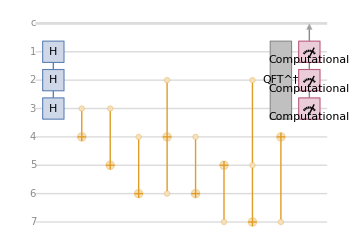

```mathematica
ShorCircuit1 = QuantumCircuitOperator[{
QuantumOperator["Hadamard",{1,2,3}],QuantumOperator["CNOT",{3,4}], QuantumOperator["CNOT",{3,5}],QuantumOperator["CNOT",{4,6}], QuantumOperator["Toffoli",{2,6,4}], QuantumOperator["CNOT",{4,6}], QuantumOperator["CNOT",{7,5}], QuantumOperator["Toffoli",{2,5,7}], QuantumOperator["CNOT",{7,4}],QuantumOperator[ QuantumOperator["InverseFourier",{1,2,3}],"Label"->"QFT^†"], QuantumMeasurementOperator["Computational",{1,2,3}]
}];
ShorCircuit1["Diagram"]
```

```mathematica
initState = QuantumTensorProduct[{QuantumState[{"Register",6}], QuantumState[{0,1}]}];
%//TraditionalForm
```

0000001

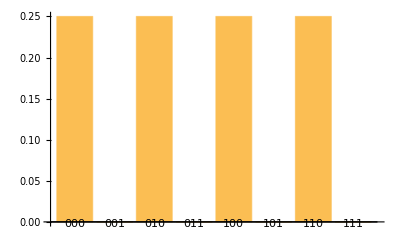

```mathematica
ShorCircuit1[initState]["ProbabilityPlot"]
```

IBM在真正的量子计算机上分解了21

对Shor算法的改进和超越

## 量子傅里叶变换的其他应用

### 隐藏子群问题 Hidden Subgroup Problem

-Graphics-

-Graphics-

隐藏子群问题：已知 f : G → X 隐藏了G的子群H，确定H ( 的生成元 )。 经典算法：计算f(G)，复杂度为O(|G|)

用量子算法解决隐藏子群问题，有限阿贝尔群的隐藏子群问题的量子算法复杂度为O(log|G|)

令 是从有限生成群  到有限集合  的映射, 满足 在子群 的同一陪集上的函数值是常数,
且在不同陪集上的函数值不同。给定一个量子黑盒执行酉变换, 
其中 是一个在 上被适当选取的二元操作, 求的一个生成集。

## 总结：需要记住的关键知识点

## 参考文献和注释

1	Quantum algorithms:
A survey of applications and end-to-end complexities

2	文中所说的“端到端”是指解决用户感兴趣的整个问题的成本，而不仅仅是运行作为完整解决方案子程序的特定量子电路的成本。

3	Quantum algorithms:
A survey of applications and end-to-end complexities

4	Quantum algorithms:
A survey of applications and end-to-end complexities

5	实际上，快速分解大数是攻破RSA公钥的方案，但是有没有可能存在其他绕开大数分解的攻克方案？换句话说，有没有可能大数分解是困难的，但是RSA却是不安全的？至少目前没有人想到这样的破解方法。

6	确定性?